```mathematica
$LifeData[[1]]
```

<|Name→Beehive,Year→1969,Class→Strict still life,Wiki→https://conwaylife.com/wiki/Procrastinator,DataFiles→{beehive.cells,beehive.rle},MatrixData→SparseArray[Automatic,{3,4},0,{1,{{0,2,4,6},{{2},{3},{1},{4},{2},{3}}},{1,1,1,1,1,1}}],InitialWeight→6|>

```mathematica
Select[$LifeData, #Class === "Spaceship"&][[1]]
```

<|Name→Glider,Year→1969,Class→Spaceship,Period→4,Speed→Rational[1,4],Wiki→https://conwaylife.com/wiki/Glider,DataFiles→{glider.cells,glider.rle},MatrixData→SparseArray[Automatic,{3,3},0,{1,{{0,1,2,5},{{2},{3},{1},{2},{3}}},{1,1,1,1,1}}],InitialWeight→5|>

```mathematica
nop = Discard[$LifeData, KeyExistsQ[#, "Period"]&];
```

```mathematica
new = If[KeyExistsQ[#, "Period"], #, ReplacePart[#, ]]
```

```mathematica
ReplacePart[<|a->1|>, Key[a]->2]
```

<|a→2|>

```mathematica
defaultValue=Missing["NotApplicable"];
filledAssoc=KeyUnion[{assoc1,assoc2,assoc3},defaultValue]
```

```mathematica
Lookup[#, {a, b, c}, 0]
```

{2,1,0}

Applicable

```mathematica
mainkeys ={"Name","Year","Class","Period","Wiki","DataFiles","MatrixData","InitialWeight"};
```

```mathematica
filled = AssociationThread[mainkeys, Lookup[#, mainkeys, Missing["NotApplicable"]]]&/@ $LifeData;
```

```mathematica
filled["Beehive"]
```

<|Name→Beehive,Year→1969,Class→Strict still life,Period→Missing[NotApplicable],Wiki→https://conwaylife.com/wiki/Procrastinator,DataFiles→{beehive.cells,beehive.rle},MatrixData→SparseArray[…],InitialWeight→6|>

```mathematica
Keys[Select[$LifeData, !KeyExistsQ[#, "Period"]&]]
```

{Beehive,Block,Crotchet,Domino,Dot,Duoplet,Line of three,Loaf,Pre-block,R-pentomino,Short table,Aircraft carrier,Banana spark,Barge,B-heptomino,Bi-block,Blockade,Boat,Bookend,Bun,Cavity,Century,C-heptomino,Claw,Crinkly heptomino,Diagonal on-off,E-heptomino,F-heptomino,Herschel,Honey farm,House,Leg,Line-of-six spark,Long barge,Long boat,Long ship,Long snake,Phi spark,Pi-heptomino,Pole 2,Pole 3,Pole 4,Pond,Queen bee,Ship,Snake,Table,Tail,Tub,V spark,Z-hexomino,Big S,Blonk-tie,Boat-bit,Breeder 1,Canoe,Cap,Cis-boat with tail,Eater 1,Flutter,Gliders by the dozen,Hat,Hook with tail,Integral sign,Iwona active region,Long canoe,Long.b3 snake,Mango,Orthogonal on-off,Pi ship 1,Shillelagh,Spiral,Squaredance,Switch engine,Thunderbird,Titanic toroidal traveler,Trans-boat with tail,Tub with tail,Twin bees shuttle spark,Two-glider octomino,U-turner,Very long boat,Very long snake,Barge siamese loaf,Beehive with tail,Block on table,Boat-tie,Boat with long tail,Broken snake,Carrier siamese carrier,Cis-barge with tail,Cis-shillelagh,Cis-very long hook with tail,Claw with tail,Four skewed blocks,Hooked integral,Long hook with tail,Long integral,Long shillelagh,Long⁴ snake,Loop,Melusine,Multum in parvo,Prodigal,RF28B,Snake siamese snake,Trans-barge with tail,Trans-very long hook with tail,Tub with long tail,Tub with very long tail,Two-glider mess,Very long shillelagh,Asymmetric amphisbaena,Barge with very long tail,Beehive at beehive,Beehive at claw,Beehive on table,Beehive with hooked tail,Beehive with nine,Block on cap,Block on cover,Boat tie eater head,Boat tie eater tail,Boat tie long boat,Boat tie long snake,Broken elevener,Bun with feather,Canoe siamese snake,Carrier bridge carrier,Carrier bridge snake,Carrier bridge table,Carrier siamese canoe,Carrier siamese hook-with-tail hook,Carrier siamese hook-with-tail tail,Carrier siamese shillelagh,Carrier siamese tub with tail,Carrier siamese very long snake,Carrier tie ship,Cis-barge with nine,Cis-block on long bookend,Cis-boat amphisbaena,Cis-boat trans-line tub,Cis-boat with long.b3 tail,Cis-carrier down on table,Cis-carrier-tie,Cis-carrier tie snake,Cis-carrier up on table,Cis-fuse with two tails,Cis-long barge with tail,Cis-long⁴ hook with tail,Cis-mango with tail,Cis-ship on table,Cis-snake-tie,Cis-tub with long⁴ tail,Cis-very long hook with nine,Claw at claw,Claw siamese tub with cape,Claw with boat with tail,Claw with nine,Double claw,Down snake on table,Eater head siamese eater head,Eater head siamese eater tail,Eater head siamese long snake,Eater tail siamese eater tail,Eater tail siamese long snake,Eater with head feather,Eater with tail feather,Egyptian walk,Fuse with tail and nine,Fuse with tail and very long tail,Fuse with two long tails,Gull with tub,Honeybarge,Hook-with-tail hook siamese snake,Hook-with-tail tail siamese snake,Hook with tail with cape,Hook with two tails,Inflexion,Integral with hook and tail,Integral with tub and tail,Long boat with long tail,Long hook line tub,Long.b3 integral,Long integral with boat,Long snake siamese long snake,Long snake with feather,Long tub-claw with tail,Rotated table,Shillelagh siamese snake,Ship tie snake,Snake bridge snake,Snake siamese very long snake,Snorkel loop,Teardrop with cape,Teardrop with claw,Trans-barge with nine,Trans-block on long bookend,Trans-boat amphisbaena,Trans-boat trans-line tub,Trans-boat with long.b3 tail,Trans-carrier down on table,Trans-carrier-tie,Trans-carrier tie snake,Trans-carrier up on table,Trans-long barge with tail,Trans-mango with tail,Trans-ship on table,Trans-snake-tie,Trans-tub with long⁴ tail,Trans-very long hook with nine,Tub bend line tub,Tub with tail siamese snake,Tub with tail with cape,Tub with two down cis tails,Tub with two down trans tails,Tub with two up cis tails,Tub with two up trans tails,Twelve loop,Up snake on table,Very long claw with tail,Very long melusine,Very long prodigal,Eater 3,Turning toads,Caber tosser 1,Cord puller,Parabolic sawtooth,Sawtooth 1212,Hacksaw,Sawtooth 1163,Sawtooth 1846,Sawtooth 362,Sawtooth 562,Sawtooth 633,Wickstretcher 1,Boatstretcher 1,Spacefiller 1,Bistable switch,Three-block shifter,Vex,Max,R64,Spacefiller 2,Conduit 1,F117,Fx119,Fx119 inserter,Fx158,Fx77,Glider stopper,Glider to block,Herschel receiver,Herschel stopper,L112,L156,p5760 unit Life cell,R190,RR56H,F116,F166,Fx153,Fx176,Herschel transmitter,HF95P,HFx58B,Jaws,Lx200,PF35W,RF48H,Rx202,Bx125,Bx222,Callahan G-to-H,Deep cell,RNE-19T84,Silver G-to-H,Silver's reflector,Catacryst,Metacatacryst,Boojum reflector,Coolout Conjecture,Quad pseudo still life,Triple pseudo still life,Blom,(13,1)c/31 Pseudo-B climber,Iwona,Justyna,23334M,7468M,Halfmax,Lidka,Moving sawtooth,One per generation,Switch engine channel,(23,5)c/79 Herschel climber,26-cell quadratic growth,Demultiplexer,F171,Honeybit,OTCA metapixel,Riley's breeder,Ship+fishhook,Four eaters,Land of lakes,35201M,Eve,p1 megacell,487-tick reflector,Rectifier,32829M,Ed,Edna,Flying wing,Fred,Sawtooth 260,1×N quadratic growth,40514M,G4 receiver,Glider to 2 blocks,R126,HLx111R,135-degree MWSS-to-G,31.4,31c/240 Herschel-pair climber,(34,7)c/156 Herschel climber,CC semi-Snark,Century eater,Pi splitter,Snark,24-cell quadratic growth,25-cell quadratic growth,c/12 R-pentomino crawler,Jaydot,Switch engine ping-pong,45-degree MWSS-to-G,B60,Beehive stopper,BLx19R,BNE14T30,BRx46B,CBx37C,G-to-LWSS,HL75P,H-to-MWSS,Quadratic sawtooth,Rx262,Sawtooth 177,Sawtooth 181,Sawtooth 201,Sidesnagger,SW1T43,Syringe,(27,1)c/72 Herschel climber,Bx106,Cloverleaf interchange,Cthulhu,Grandfather problem,Professor,Scorbie Splitter,24827M,CC semi-cenark,CP semi-cenark,CP semi-Snark,F131,Quadri-Snark,Tremi-Snark,42100M,Bronco,Homer,Jormungant's G-to-H,Wilma,47575M,R49,49768M,Bandersnatch,Beehive push catalyst,L122,50093M,52513M,p4 syringe,20-cell quadratic growth,21-cell quadratic growth,22-cell quadratic growth,Chucklebait,CL48C,HRx65R,HRx74B,NW-2T16,Quartermax,Speed tunnel,Unique father problem,0-degree colour-preserving reflector (March 2023),G-to-LWSS (2023),G-to-pi catalyst (August 2023),Snark64,135-degree LWSS-to-G,L141,Lx65 duplicator,Spartan G-to-W-to-H}

```mathematica
Keys[$LifeData["Gosper glider gun"]]
```

{Name,Year,Class,Period,Wiki,DataFiles,MatrixData,InitialWeight}

f

```mathematica
filled["Chucklebait"]
```

<|Name→Chucklebait,Year→2022,Class→Strict still life,Period→Missing[NotApplicable],Wiki→https://conwaylife.com/wiki/Chucklebait,DataFiles→{chucklebait.cells,chucklebait.rle},MatrixData→SparseArray[…],InitialWeight→23|>

```mathematica
fn =ReplacePart[filled, Key["Chucklebait"]-> Merge[{filled["Chucklebait"], <|"Class"->"Strict still life"|>},Last]];
```

```mathematica
fn["Chucklebait"]
```

<|Name→Chucklebait,Year→2022,Class→Strict still life,Period→Missing[NotApplicable],Wiki→https://conwaylife.com/wiki/Chucklebait,DataFiles→{chucklebait.cells,chucklebait.rle},MatrixData→SparseArray[…],InitialWeight→23|>

```mathematica
fn = AssociateTo[filled, "Chucklebait"-> AssociateTo[filled["Chucklebait"], "Class"->"Strict still life"]];
```

```mathematica
Head@fn
```

Association

```mathematica
fn["Glider"]
```

<|Name→Glider,Year→1969,Class→Spaceship,Period→4,Wiki→https://conwaylife.com/wiki/Glider,DataFiles→{glider.cells,glider.rle},MatrixData→SparseArray[…],InitialWeight→5|>

```mathematica
fn["Chucklebait"]
```

$Aborted

```mathematica
CellularAutomatonPlot3D["GameOfLife", {#MatrixData, 0}, 20]&@filled["Chucklebait"]
```

-Graphics3D-

```mathematica
"Period-16 glider gun"-><|"Name"->"Period-16 glider gun","Year"->2024,"Period"->16,"Class"->"Gun","Wiki"->"https://conwaylife.com/wiki/Period-16_glider_gun","DataFiles"->{"period16glidergun.rle"},"MatrixData"->SparseArray[…]|>
```

```mathematica
Join[$LifeData/@{"Gosper glider gun","Period-60 glider gun","New gun 1","Period-24 glider gun","Period-44 glider gun","Vacuum (gun)","Period-22 glider gun","Period-88 glider gun","Period-45 glider gun","AK-94","Period-92 glider gun","Period-33 glider gun","Period-54 glider gun","Period-55 glider gun","P16-assisted period-32 glider gun","p4-assisted period-28 glider gun","Period-25 glider gun","Period-27 glider gun","Period-34 glider gun","Period-43 glider gun","Period-48 glider gun","Period-51 glider gun","Period-41 glider gun","Period-49 glider gun (April 2023)","Period-61 glider gun (2023)","Period-36 glider gun","Period-53 glider gun"},
{<|"MatrixData"->SparseArray[…],"Period"->15,"Year"->2024|>,
<|"MatrixData"->SparseArray[…],"Period"->16,"Year"->2024|>,
<|"MatrixData"->SparseArray[…],"Period"->20,"Year"->2021|>,
<|"MatrixData"->SparseArray[…],"Period"->21,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->35,"Year"->2025|>,
<|"MatrixData"->SparseArray[…],"Period"->37,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->40,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->47,"Year"->2025|>}][[-3;;]]
```

{<|MatrixData→SparseArray[…],Period→37,Year→2022|>,<|MatrixData→SparseArray[…],Period→40,Year→2022|>,<|MatrixData→SparseArray[…],Period→47,Year→2025|>}

Need to figure out where these came from and what their names are

```mathematica
Labeled[ArrayPlot[#MatrixData], {#Year, #Period}]&/@ SortBy[sas, #Year&]
```

{-Graphics-{2021,20},-Graphics-{2022,40},-Graphics-{2022,21},-Graphics-{2022,37},-Graphics-{2024,16},-Graphics-{2024,15},-Graphics-{2025,47},-Graphics-{2025,35}}

```mathematica
{"https://conwaylife.com/wiki/Period-20_glider_gun","https://conwaylife.com/wiki/Period-40_glider_gun","https://conwaylife.com/wiki/P21_B-heptomino_hassler#Guns","https://conwaylife.com/wiki/58P37","https://conwaylife.com/wiki/Period-16_glider_gun", "https://conwaylife.com/wiki/Period-15_glider_gun", "https://conwaylife.com/wiki/Period-47_glider_gun", "https://conwaylife.com/wiki/Period-35_glider_gun"}
```

```mathematica
sas = {<|"MatrixData"->SparseArray[…],"Period"->15,"Year"->2024|>,
<|"MatrixData"->SparseArray[…],"Period"->16,"Year"->2024|>,
<|"MatrixData"->SparseArray[…],"Period"->20,"Year"->2021|>,
<|"MatrixData"->SparseArray[…],"Period"->21,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->35,"Year"->2025|>,
<|"MatrixData"->SparseArray[…],"Period"->37,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->40,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->47,"Year"->2025|>};
```

```mathematica
HoldForm[Key[#]]&/@{"Gosper glider gun","Period-60 glider gun","New gun 1","Period-24 glider gun","Period-44 glider gun","Vacuum (gun)","Period-22 glider gun","Period-88 glider gun","Period-45 glider gun","AK-94","Period-92 glider gun","Period-33 glider gun","Period-54 glider gun","Period-55 glider gun","P16-assisted period-32 glider gun","p4-assisted period-28 glider gun","Period-25 glider gun","Period-27 glider gun","Period-34 glider gun","Period-43 glider gun","Period-48 glider gun","Period-51 glider gun","Period-41 glider gun","Period-49 glider gun (April 2023)","Period-61 glider gun (2023)","Period-36 glider gun","Period-53 glider gun"}
```

{Key[Gosper glider gun],Key[Period-60 glider gun],Key[New gun 1],Key[Period-24 glider gun],Key[Period-44 glider gun],Key[Vacuum (gun)],Key[Period-22 glider gun],Key[Period-88 glider gun],Key[Period-45 glider gun],Key[AK-94],Key[Period-92 glider gun],Key[Period-33 glider gun],Key[Period-54 glider gun],Key[Period-55 glider gun],Key[P16-assisted period-32 glider gun],Key[p4-assisted period-28 glider gun],Key[Period-25 glider gun],Key[Period-27 glider gun],Key[Period-34 glider gun],Key[Period-43 glider gun],Key[Period-48 glider gun],Key[Period-51 glider gun],Key[Period-41 glider gun],Key[Period-49 glider gun (April 2023)],Key[Period-61 glider gun (2023)],Key[Period-36 glider gun],Key[Period-53 glider gun]}

```mathematica
names = {"Gosper glider gun","Period-60 glider gun","New gun 1","Period-24 glider gun","Period-44 glider gun","Vacuum (gun)","Period-22 glider gun","Period-88 glider gun","Period-45 glider gun","AK-94","Period-92 glider gun","Period-33 glider gun","Period-54 glider gun","Period-55 glider gun","P16-assisted period-32 glider gun","p4-assisted period-28 glider gun","Period-25 glider gun","Period-27 glider gun","Period-34 glider gun","Period-43 glider gun","Period-48 glider gun","Period-51 glider gun","Period-41 glider gun","Period-49 glider gun (April 2023)","Period-61 glider gun (2023)","Period-36 glider gun","Period-53 glider gun"};
```

```mathematica
Length[sas]
```

8

```mathematica
Length[names]
```

27

```mathematica
rus = MapThread[#1->Join[ fn[#1], #2]&, {sas,names}];
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of …; dimensions are 8 and 27.

```mathematica
ReplacePart[]
```

```mathematica
ReplacePart[Key[]]
```

```mathematica
Join[<|a->1|>, <|a->2|>]
```

<|a→2|>

```mathematica
sas[[-1]]
```

<|MatrixData→SparseArray[…],Period→47,Year→2025|>

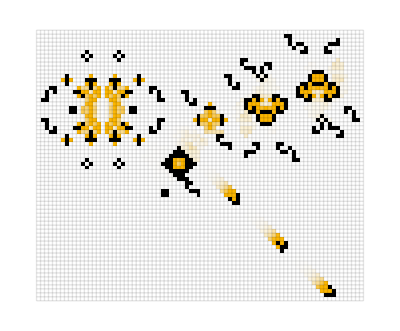

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData, 0}, 100]&@sas[[-1]]
```

### Adding glider guns

```mathematica
urls = {"https://conwaylife.com/wiki/Period-20_glider_gun","https://conwaylife.com/wiki/Period-40_glider_gun","https://conwaylife.com/wiki/P21_B-heptomino_hassler#Guns","https://conwaylife.com/wiki/58P37","https://conwaylife.com/wiki/Period-16_glider_gun", "https://conwaylife.com/wiki/Period-15_glider_gun", "https://conwaylife.com/wiki/Period-47_glider_gun", "https://conwaylife.com/wiki/Period-35_glider_gun"};
```

```mathematica
xs = Import[#, "XML"]&/@ urls;
```

Import::nfprserr: element name expected at line: 1 character: 753 in /private/var/folders/_1/8j0kws797tg83z3r45c_770h0000gp/T/m00004392131/Period-20_glider_gun.

Import::nfprserr: element name expected at line: 1 character: 753 in /private/var/folders/_1/8j0kws797tg83z3r45c_770h0000gp/T/m00004492131/Period-40_glider_gun.

Import::nfprserr: element name expected at line: 1 character: 753 in /private/var/folders/_1/8j0kws797tg83z3r45c_770h0000gp/T/m00004592131.

General::stop: Further output of Import::nfprserr will be suppressed during this calculation.

```mathematica
names={"Period-20 glider gun","Period-40 glider gun","P21 B-heptomino hassler","58P37","Period-16 glider gun","Period-15 glider gun","Period-47 glider gun","Period-35 glider gun"};
```

```mathematica
ggs = Association[MapThread[#1->Join[<|"Name"->#1, "Wiki"-> #2|>, #3]&, {names, urls, SortBy[sas, #Year&]}]]
```

<|Period-20 glider gun→<|Name→Period-20 glider gun,Wiki→https://conwaylife.com/wiki/Period-20_glider_gun,MatrixData→SparseArray[…],Period→20,Year→2021|>,Period-40 glider gun→<|Name→Period-40 glider gun,Wiki→https://conwaylife.com/wiki/Period-40_glider_gun,MatrixData→SparseArray[…],Period→40,Year→2022|>,P21 B-heptomino hassler→<|Name→P21 B-heptomino hassler,Wiki→https://conwaylife.com/wiki/P21_B-heptomino_hassler#Guns,MatrixData→SparseArray[…],Period→21,Year→2022|>,58P37→<|Name→58P37,Wiki→https://conwaylife.com/wiki/58P37,MatrixData→SparseArray[…],Period→37,Year→2022|>,Period-16 glider gun→<|Name→Period-16 glider gun,Wiki→https://conwaylife.com/wiki/Period-16_glider_gun,MatrixData→SparseArray[…],Period→16,Year→2024|>,Period-15 glider gun→<|Name→Period-15 glider gun,Wiki→https://conwaylife.com/wiki/Period-15_glider_gun,MatrixData→SparseArray[…],Period→15,Year→2024|>,Period-47 glider gun→<|Name→Period-47 glider gun,Wiki→https://conwaylife.com/wiki/Period-47_glider_gun,MatrixData→SparseArray[…],Period→47,Year→2025|>,Period-35 glider gun→<|Name→Period-35 glider gun,Wiki→https://conwaylife.com/wiki/Period-35_glider_gun,MatrixData→SparseArray[…],Period→35,Year→2025|>|>

```mathematica
ld2 = AppendTo[$LifeData, ggs];
```

```mathematica
ld2["Period-35 glider gun"]
```

<|Name→Period-35 glider gun,Wiki→https://conwaylife.com/wiki/Period-35_glider_gun,MatrixData→SparseArray[…],Period→47,Year→2025|>

### outtake

```mathematica
With[{byy = Total/@GroupBy[Catenate[byp], #Year&->(Times@@Dimensions[#MatrixData]&)]}, 
Table[Lookup[byy, i, 0], {i, 1969, 2025}]]
```

{52,932,3168,3244,4518,0,0,1002,1237,1130,256,1283,0,1100,2303,6767,1282,1161,0,177,2301,1318,0,3920,2908,15826,10292,1188,446848,3907,4511,1873,0,3643,1110,82131,1393,100,2325,2791,5895,7502,4066,6431,4885,3205,3400,3093,548,6067,41026,486,32497,94015,131960,10767,0}

```mathematica
GroupBy[Catenate[byp], #Year&->(Times@@Dimensions[#MatrixData]&)][1997]
```

{700,160,72,165,432,72,100,130,195,759,180,1519,1332,111556,329476}

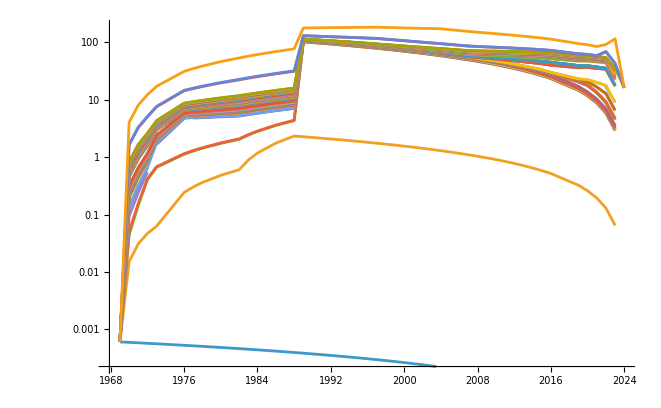

```mathematica
ListLinePlot[MapIndexed[{#Year, Times@@Dimensions[#MatrixData]}&, allis, {2}],  PlotLayout->"Percentile", ScalingFunctions->"Log"]
```

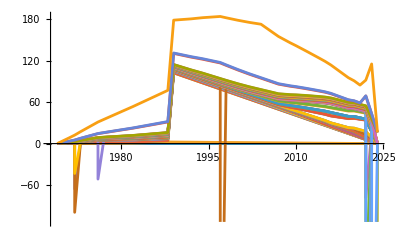

```mathematica
ListLinePlot[MapIndexed[{#Year, Times@@Dimensions[#MatrixData]}&, allis, {2}],  PlotLayout->"Percentile"]
```